Инициализация...

Mathematica version is 10. Assigning RotationMatrix3D and BlockMatrix

Loading modules ...

Mathematica version is 10. Assigning OFULL via Join.

... completed.

==============================================

BM version: 6.02.001

Release date: 2016/04/12

Crystal Plate Reflection and Transmission. .

BerremanInitVersion = 6.02
BerremanCommonVersion = 6.02
BerremanDirectVersion = 6.02
BerremanInverseVersion = 5.03
FieldAlgebraVersion = 6.02
FieldIOVersion = 6.02
FieldIOFormatVersion = 6.02

Copyright: K^3, 2001 - 2016.

Email: konstantin.k.konstantinov@gmail.com

License type: GPL v3 or any later version, see http://www.gnu.org/licenses/

==============================================

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version. This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General Public License for more details. You should have received a copy of the GNU General Public License along with this program. If not, see http://www.gnu.org/licenses/ .

==============================================

Инициализация завершена.

==============================================

!!! For absorbing plate I > R + T !!!

Параметры падающего света...

Upper refractive index n_u = 1, parameters: (600 | 600 | 1 | λ | 1/1000000000
0 | 85 | 5 | ϕ | °
0 | 0 | 45 | β | °
-1 | 1 | 0.5 | e | )

---------------------------------------------

Оптические параметры первого тонкого слоя.

epsLayer1 = (2.25 | 0 | 0
0 | 4. | 0
0 | 0 | 3.0625)

Оптические параметры толстой пластинки

Для расчетов для различных толщин пластинки нужно поменять значение thickness

Оптические параметры нижней среды...

Создаем оптическую систему...

---

Layered System = {LayeredSystem,{{1,1.5+3.×10^-6 ⅈ,{0,0,30,γ,°},{{0,{{2.25,0,0},{0,4.,0},{0,0,3.0625}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{2.25,0,0},{0,4.,0},{0,0,3.0625}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}},,1.5,1/1000,{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{2.25+9.×10^-6 ⅈ,0,0},{0,2.25+9.×10^-6 ⅈ,0},{0,0,2.25+9.×10^-6 ⅈ}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}},{{600,600,1,λ,1/1000000000},{0,85,5,ϕ,°},{0,0,45,β,°},{0,0,30,γ,°},{-1,1,0.5,e},{0,0,1,φ_2,°},{0,0,1,θ_2,°},{0,0,1,ψ_2,°},{0,0,30,φ_1,°},{0,0,30,θ_1,°},{0,0,30,ψ_1,°},{75,75,10,h,1/1000000000}},{UseThickLastLayer→True}}}

==============================================

Производим вычисления для различных значений параметров....

PerformAllCalculations::Calculating...

Start time: 0:39:23

Total number of points to calculate: 90

Estimated total calculation time: 0:00:20

Estimated end time: 0:39:44

==============================================

Using Optiva angles for rotation: 
Rotation 1: Fi (angle between crystal axis and deposition direction) - rotation around z; 
Rotation 2: Psi (angle between crystal axis and substrate plane.) - rotation around y (in the opposite direction!!!); 
Rotation 3: Alpha (rotation of crystal around its axis.) - rotation around x.

==============================================

==============================================

Printing Collection...

==============================================

*** Multilayered Thin Film Output File Format Version 6.02 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Modelling Engine Version 6.02 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
* Description * |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
One Layer biaxial thin film on slighlty absorbing substrate plate. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using Media Orientation Angles. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Solving for layered film on a THICK SUBSTRATE plate. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 100 |     Averaging Type:  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 5 |     No Of Averaging Points:  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |     Averaging Periods:  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Rotating all layers simultaneously. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using consecutive rotations. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | AbsoluteAzimuth | Using Absolute Azimuth |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Refraction_Index |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |  | 1.5+3.×10^-6 ⅈ |  | 1.5 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Begin Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | Epsilon RE |  |  |  | Epsilon IM |  |  |  | Mu RE |  |  |  | Mu IM |  |  |  | Ro RE |  |  |  | Ro IM |  |  |  | RoT RE |  |  |  | RoT IM |  |  | 
 | 2.25 | 0 | 0 |  | 9.×10^-6 | 0 | 0 |  | 1 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
 | 0 | 2.25 | 0 |  | 0 | 9.×10^-6 | 0 |  | 0 | 1 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
 | 0 | 0 | 2.25 |  | 0 | 0 | 9.×10^-6 |  | 0 | 0 | 1 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
** End Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Thickness |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Nothing to ouput so far... |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
n |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1.5 | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0. | 2. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0. | 0. | 1.75 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
k |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_RE |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 2.25 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 4. | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 3.0625 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_IM |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Output Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

(Input | No | λ | ϕ | β | γ | e | φ_2 | θ_2 | ψ_2 | φ_1 | θ_1 | ψ_1 | h | Output | S_(R,0) | S_(R,1) | S_(R,2) | S_(R,3) | R | T | γ_R | ° γ_R | χ_R | ° χ_R | p_R | χ_r | e_r | ψ_pp | Δ_pp | R_p | R_s | T_p | T_s
 | 1. | 600. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.123306 | -0.0833059 | -1.49879×10^-7 | 0.0909088 | 0.123306 | 0.823305 | 0.414506 | 23.7494 | 0.785399 | 45. | 1. | -89.9999 | 0.439999 | 23.7494 | 180. | 0.0199999 | 0.103306 | 0.450769 | 0.372536
 | 2. | 600. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0733221 | -0.00932253 | -1.19903×10^-7 | 0.072727 | 0.0733221 | 0.870244 | 0.721653 | 41.3477 | 0.785399 | 45. | 1. | -89.9996 | 0.879997 | 23.7494 | 180. | 0.0319998 | 0.0413223 | 0.72123 | 0.149014
 | 3. | 600. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0399997 | 0.0399997 | 0. | 0. | 0.0399997 | 0.901538 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 23.7494 | 180. | 0.0399997 | 0. | 0.901538 | 0.
 | 4. | 600. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0733221 | -0.00932253 | 1.19903×10^-7 | -0.072727 | 0.0733221 | 0.870244 | -0.721653 | -41.3477 | -0.785397 | -45. | 1. | 89.9996 | -0.879997 | 23.7494 | 180. | 0.0319998 | 0.0413223 | 0.72123 | 0.149014
 | 5. | 600. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.123306 | -0.0833059 | 1.49879×10^-7 | -0.0909088 | 0.123306 | 0.823305 | -0.414506 | -23.7494 | -0.785397 | -45. | 1. | 89.9999 | -0.439999 | 23.7494 | 180. | 0.0199999 | 0.103306 | 0.450769 | 0.372536
 | 6. | 600. | 5. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.123679 | -0.0842322 | 0.000138256 | 0.0905621 | 0.123679 | 0.822866 | 0.410798 | 23.537 | 0.784635 | 44.9563 | 1. | 89.953 | 0.43558 | 23.537 | 179.956 | 0.0197236 | 0.103956 | 0.45098 | 0.371886
 | 7. | 600. | 5. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.07314 | -0.0100246 | 0.000110605 | 0.0724497 | 0.07314 | 0.870323 | 0.716647 | 41.0609 | 0.784635 | 44.9563 | 1. | 89.6839 | 0.871154 | 23.537 | 179.956 | 0.0315577 | 0.0415823 | 0.721568 | 0.148754
 | 8. | 600. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0394471 | 0.0394471 | 0. | 0. | 0.0394471 | 0.901961 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 23.537 | 179.956 | 0.0394471 | 0. | 0.901961 | 0.
 | 9. | 600. | 5. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.07314 | -0.0100246 | -0.000110605 | -0.0724497 | 0.07314 | 0.870323 | -0.716647 | -41.0609 | -0.786161 | -45.0437 | 1. | -89.6839 | -0.871154 | 23.537 | 179.956 | 0.0315577 | 0.0415823 | 0.721568 | 0.148754
 | 10. | 600. | 5. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.123679 | -0.0842322 | -0.000138256 | -0.0905621 | 0.123679 | 0.822866 | -0.410798 | -23.537 | -0.786161 | -45.0437 | 1. | -89.953 | -0.43558 | 23.537 | 179.956 | 0.0197236 | 0.103956 | 0.45098 | 0.371886
 | 11. | 600. | 10. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.124823 | -0.0870245 | 0.000552646 | 0.0894824 | 0.124823 | 0.821531 | 0.399656 | 22.8986 | 0.78231 | 44.8231 | 1. | 89.8181 | 0.422388 | 22.8992 | 179.828 | 0.018899 | 0.105924 | 0.45161 | 0.36992
 | 12. | 600. | 10. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0726078 | -0.012131 | 0.000442117 | 0.0715859 | 0.0726078 | 0.870545 | 0.701411 | 40.1879 | 0.78231 | 44.8231 | 1. | 88.9564 | 0.844703 | 22.8992 | 179.828 | 0.0302384 | 0.0423694 | 0.722577 | 0.147968
 | 13. | 600. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.037798 | 0.037798 | 0. | 0. | 0.037798 | 0.903221 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 22.8992 | 179.828 | 0.037798 | 0. | 0.903221 | 0.
 | 14. | 600. | 10. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0726078 | -0.012131 | -0.000442117 | -0.0715859 | 0.0726078 | 0.870545 | -0.701411 | -40.1879 | -0.788486 | -45.1769 | 1. | -88.9564 | -0.844703 | 22.8992 | 179.828 | 0.0302384 | 0.0423694 | 0.722577 | 0.147968
 | 15. | 600. | 10. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.124823 | -0.0870245 | -0.000552646 | -0.0894824 | 0.124823 | 0.821531 | -0.399656 | -22.8986 | -0.788486 | -45.1769 | 1. | -89.8181 | -0.422388 | 22.8992 | 179.828 | 0.018899 | 0.105924 | 0.45161 | 0.36992
 | 16. | 600. | 15. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.126804 | -0.091723 | 0.00124014 | 0.0875479 | 0.126804 | 0.819235 | 0.381034 | 21.8316 | 0.778316 | 44.5942 | 1. | 89.6127 | 0.400612 | 21.8344 | 179.622 | 0.0175406 | 0.109264 | 0.452645 | 0.36659
 | 17. | 600. | 15. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0717703 | -0.0156405 | 0.000992115 | 0.0700383 | 0.0717703 | 0.870868 | 0.67533 | 38.6936 | 0.778316 | 44.5942 | 1. | 88.1852 | 0.800966 | 21.8344 | 179.622 | 0.0280649 | 0.0437054 | 0.724232 | 0.146636
 | 18. | 600. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0350811 | 0.0350811 | 0. | 0. | 0.0350811 | 0.90529 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 21.8344 | 179.622 | 0.0350811 | 0. | 0.90529 | 0.
 | 19. | 600. | 15. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0717703 | -0.0156405 | -0.000992115 | -0.0700383 | 0.0717703 | 0.870868 | -0.67533 | -38.6936 | -0.79248 | -45.4058 | 1. | -88.1852 | -0.800966 | 21.8344 | 179.622 | 0.0280649 | 0.0437054 | 0.724232 | 0.146636
 | 20. | 600. | 15. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.126804 | -0.091723 | -0.00124014 | -0.0875479 | 0.126804 | 0.819235 | -0.381034 | -21.8316 | -0.79248 | -45.4058 | 1. | -89.6127 | -0.400612 | 21.8344 | 179.622 | 0.0175406 | 0.109264 | 0.452645 | 0.36659
 | 21. | 600. | 20. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.129744 | -0.0983916 | 0.00219469 | 0.0845449 | 0.129744 | 0.81587 | 0.354864 | 20.3322 | 0.772422 | 44.2565 | 1. | 89.3611 | 0.37055 | 20.3405 | 179.349 | 0.0156763 | 0.114068 | 0.454057 | 0.361814
 | 22. | 600. | 20. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0707093 | -0.0205451 | 0.00175575 | 0.0676359 | 0.0707093 | 0.871216 | 0.63744 | 36.5226 | 0.772422 | 44.2565 | 1. | 87.5577 | 0.740573 | 20.3405 | 179.349 | 0.0250821 | 0.0456272 | 0.72649 | 0.144726
 | 23. | 600. | 20. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0313526 | 0.0313526 | 0. | 0. | 0.0313526 | 0.908113 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 20.3405 | 179.349 | 0.0313526 | 0. | 0.908113 | 0.
 | 24. | 600. | 20. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0707093 | -0.0205451 | -0.00175575 | -0.0676359 | 0.0707093 | 0.871216 | -0.63744 | -36.5226 | -0.798375 | -45.7435 | 1. | -87.5577 | -0.740573 | 20.3405 | 179.349 | 0.0250821 | 0.0456272 | 0.72649 | 0.144726
 | 25. | 600. | 20. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.129744 | -0.0983916 | -0.00219469 | -0.0845449 | 0.129744 | 0.81587 | -0.354864 | -20.3322 | -0.798375 | -45.7435 | 1. | -89.3611 | -0.37055 | 20.3405 | 179.349 | 0.0156763 | 0.114068 | 0.454057 | 0.361814
 | 26. | 600. | 25. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.133824 | -0.107113 | 0.00340517 | 0.0801501 | 0.133824 | 0.811272 | 0.321077 | 18.3964 | 0.764168 | 43.7836 | 1. | 89.0896 | 0.332585 | 18.4157 | 179.023 | 0.0133554 | 0.120469 | 0.455798 | 0.355474
 | 27. | 600. | 25. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0695561 | -0.0268188 | 0.00272414 | 0.0641201 | 0.0695561 | 0.871466 | 0.58641 | 33.5988 | 0.764168 | 43.7836 | 1. | 87.1 | 0.664368 | 18.4157 | 179.023 | 0.0213687 | 0.0481875 | 0.729277 | 0.14219
 | 28. | 600. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0267109 | 0.0267109 | 0. | 0. | 0.0267109 | 0.911596 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 18.4157 | 179.023 | 0.0267109 | 0. | 0.911596 | 0.
 | 29. | 600. | 25. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0695561 | -0.0268188 | -0.00272414 | -0.0641201 | 0.0695561 | 0.871466 | -0.58641 | -33.5988 | -0.806628 | -46.2164 | 1. | -87.1 | -0.664368 | 18.4157 | 179.023 | 0.0213687 | 0.0481875 | 0.729277 | 0.14219
 | 30. | 600. | 25. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.133824 | -0.107113 | -0.00340517 | -0.0801501 | 0.133824 | 0.811272 | -0.321077 | -18.3964 | -0.806628 | -46.2164 | 1. | -89.0896 | -0.332585 | 18.4157 | 179.023 | 0.0133554 | 0.120469 | 0.455798 | 0.355474
 | 31. | 600. | 30. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.139301 | -0.11798 | 0.00485299 | 0.0739039 | 0.139301 | 0.805209 | 0.279615 | 16.0208 | 0.752612 | 43.1215 | 1. | 88.8223 | 0.287138 | 16.0594 | 178.665 | 0.0106602 | 0.128641 | 0.457792 | 0.347417
 | 32. | 600. | 30. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0685125 | -0.0344 | 0.00388239 | 0.0591231 | 0.0685125 | 0.871433 | 0.520542 | 29.8249 | 0.752612 | 43.1215 | 1. | 86.7804 | 0.573282 | 16.0594 | 178.665 | 0.0170563 | 0.0514563 | 0.732466 | 0.138967
 | 33. | 600. | 30. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0213204 | 0.0213204 | 0. | 0. | 0.0213204 | 0.915583 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 16.0594 | 178.665 | 0.0213204 | 0. | 0.915583 | 0.
 | 34. | 600. | 30. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0685125 | -0.0344 | -0.00388239 | -0.0591231 | 0.0685125 | 0.871433 | -0.520542 | -29.8249 | -0.818184 | -46.8785 | 1. | -86.7804 | -0.573282 | 16.0594 | 178.665 | 0.0170563 | 0.0514563 | 0.732466 | 0.138967
 | 35. | 600. | 30. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.139301 | -0.11798 | -0.00485299 | -0.0739039 | 0.139301 | 0.805209 | -0.279615 | -16.0208 | -0.818184 | -46.8785 | 1. | -88.8223 | -0.287138 | 16.0594 | 178.665 | 0.0106602 | 0.128641 | 0.457792 | 0.347417
 | 36. | 600. | 35. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.146531 | -0.131079 | 0.00650911 | 0.0651694 | 0.146531 | 0.797363 | 0.230447 | 13.2037 | 0.735623 | 42.1481 | 1. | 88.5786 | 0.234615 | 13.2745 | 178.297 | 0.00772563 | 0.138805 | 0.459913 | 0.33745
 | 37. | 600. | 35. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.067883 | -0.043161 | 0.00520729 | 0.0521355 | 0.067883 | 0.87084 | 0.437872 | 25.0882 | 0.735623 | 42.1481 | 1. | 86.5603 | 0.468184 | 13.2745 | 178.297 | 0.012361 | 0.055522 | 0.73586 | 0.13498
 | 38. | 600. | 35. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0154513 | 0.0154513 | 0. | 0. | 0.0154513 | 0.919825 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 13.2745 | 178.297 | 0.0154513 | 0. | 0.919825 | 0.
 | 39. | 600. | 35. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.067883 | -0.043161 | -0.00520729 | -0.0521355 | 0.067883 | 0.87084 | -0.437872 | -25.0882 | -0.835173 | -47.8519 | 1. | -86.5603 | -0.468184 | 13.2745 | 178.297 | 0.012361 | 0.055522 | 0.73586 | 0.13498
 | 40. | 600. | 35. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.146531 | -0.131079 | -0.00650911 | -0.0651694 | 0.146531 | 0.797363 | -0.230447 | -13.2037 | -0.835173 | -47.8519 | 1. | -88.5786 | -0.234615 | 13.2745 | 178.297 | 0.00772563 | 0.138805 | 0.459913 | 0.33745
 | 41. | 600. | 40. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.156004 | -0.146461 | 0.00833096 | 0.0530752 | 0.156004 | 0.787299 | 0.173574 | 9.94505 | 0.707551 | 40.5397 | 1. | 88.3722 | 0.175338 | 10.0721 | 177.945 | 0.00477143 | 0.151232 | 0.46196 | 0.325338
 | 42. | 600. | 40. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0681273 | -0.0528587 | 0.00666476 | 0.0424601 | 0.0681273 | 0.869272 | 0.336444 | 19.2768 | 0.707551 | 40.5397 | 1. | 86.4069 | 0.349741 | 10.0721 | 177.945 | 0.00763429 | 0.060493 | 0.739137 | 0.130135
 | 43. | 600. | 40. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.00954286 | 0.00954286 | 0. | 0. | 0.00954286 | 0.923921 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 10.0721 | 177.945 | 0.00954286 | 0. | 0.923921 | 0.
 | 44. | 600. | 40. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0681273 | -0.0528587 | -0.00666476 | -0.0424601 | 0.0681273 | 0.869272 | -0.336444 | -19.2768 | -0.863246 | -49.4603 | 1. | -86.4069 | -0.349741 | 10.0721 | 177.945 | 0.00763429 | 0.060493 | 0.739137 | 0.130135
 | 45. | 600. | 40. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.156004 | -0.146461 | -0.00833096 | -0.0530752 | 0.156004 | 0.787299 | -0.173574 | -9.94505 | -0.863246 | -49.4603 | 1. | -88.3722 | -0.175338 | 10.0721 | 177.945 | 0.00477143 | 0.151232 | 0.46196 | 0.325338
 | 46. | 600. | 45. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.168402 | -0.164094 | 0.0102593 | 0.0364306 | 0.168402 | 0.774413 | 0.109028 | 6.24683 | 0.648146 | 37.136 | 1. | 88.2112 | 0.109462 | 6.49397 | 177.637 | 0.00215408 | 0.166248 | 0.463611 | 0.310801
 | 47. | 600. | 45. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0699456 | -0.0630526 | 0.00820748 | 0.0291445 | 0.0699456 | 0.866098 | 0.214892 | 12.3124 | 0.648146 | 37.136 | 1. | 86.2918 | 0.218262 | 6.49397 | 177.637 | 0.00344653 | 0.0664991 | 0.741778 | 0.124321
 | 48. | 600. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.00430816 | 0.00430816 | 0. | 0. | 0.00430816 | 0.927222 | 0. | 0. | 0. | 0. | 1. | 8.53774×10^-7 | 0. | 6.49397 | 177.637 | 0.00430816 | 0. | 0.927222 | 0.
 | 49. | 600. | 45. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0699456 | -0.0630526 | -0.00820748 | -0.0291445 | 0.0699456 | 0.866098 | -0.214892 | -12.3124 | -0.92265 | -52.864 | 1. | -86.2918 | -0.218262 | 6.49397 | 177.637 | 0.00344653 | 0.0664991 | 0.741778 | 0.124321
 | 50. | 600. | 45. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.168402 | -0.164094 | -0.0102593 | -0.0364306 | 0.168402 | 0.774413 | -0.109028 | -6.24683 | -0.92265 | -52.864 | 1. | -88.2112 | -0.109462 | 6.49397 | 177.637 | 0.00215408 | 0.166248 | 0.463611 | 0.310801
 | 51. | 600. | 50. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.184686 | -0.183778 | 0.0122158 | 0.0136052 | 0.184686 | 0.757856 | 0.0368668 | 2.11231 | 0.419578 | 24.0401 | 1. | 88.0986 | 0.0368836 | 2.84091 | 177.402 | 0.000453677 | 0.184232 | 0.464341 | 0.293515
 | 52. | 600. | 50. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0744187 | -0.0729669 | 0.00977262 | 0.0108842 | 0.0744187 | 0.860352 | 0.0733912 | 4.20501 | 0.419578 | 24.0401 | 1. | 86.1858 | 0.0735233 | 2.84091 | 177.402 | 0.000725883 | 0.0736928 | 0.742946 | 0.117406
 | 53. | 600. | 50. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.000907353 | 0.000907353 | 0. | 0. | 0.000907353 | 0.928683 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 2.84091 | 177.402 | 0.000907353 | 0. | 0.928683 | 0.
 | 54. | 600. | 50. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0744187 | -0.0729669 | -0.00977262 | -0.0108842 | 0.0744187 | 0.860352 | -0.0733912 | -4.20501 | -1.15122 | -65.9599 | 1. | -86.1858 | -0.0735233 | 2.84091 | 177.402 | 0.000725883 | 0.0736928 | 0.742946 | 0.117406
 | 55. | 600. | 50. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.184686 | -0.183778 | -0.0122158 | -0.0136052 | 0.184686 | 0.757856 | -0.0368668 | -2.11231 | -1.15122 | -65.9599 | 1. | -88.0986 | -0.0368836 | 2.84091 | 177.402 | 0.000453677 | 0.184232 | 0.464341 | 0.293515
 | 56. | 600. | 55. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.206245 | -0.205004 | 0.0140996 | -0.0176472 | 0.206245 | 0.736399 | -0.0428345 | -2.45424 | -0.448342 | -25.6881 | 1. | 88.0328 | -0.0428608 | 3.14385 | 177.267 | 0.000620332 | 0.205624 | 0.463295 | 0.273104
 | 57. | 600. | 55. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0832423 | -0.0812573 | 0.0112797 | -0.0141178 | 0.0832423 | 0.850513 | -0.0852111 | -4.88223 | -0.448342 | -25.6881 | 1. | 86.0485 | -0.0854179 | 3.14385 | 177.267 | 0.000992532 | 0.0822498 | 0.741271 | 0.109242
 | 58. | 600. | 55. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.00124066 | 0.00124066 | 0. | 0. | 0.00124066 | 0.926589 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 3.14385 | 177.267 | 0.00124066 | 0. | 0.926589 | 0.
 | 59. | 600. | 55. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0832423 | -0.0812573 | -0.0112797 | 0.0141178 | 0.0832423 | 0.850513 | 0.0852111 | 4.88223 | 1.12245 | 64.3119 | 1. | -86.0485 | 0.0854179 | 3.14385 | 177.267 | 0.000992532 | 0.0822498 | 0.741271 | 0.109242
 | 60. | 600. | 55. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.206245 | -0.205004 | -0.0140996 | 0.0176472 | 0.206245 | 0.736399 | 0.0428345 | 2.45424 | 1.12245 | 64.3119 | 1. | -88.0328 | 0.0428608 | 3.14385 | 177.267 | 0.000620332 | 0.205624 | 0.463295 | 0.273104
 | 61. | 600. | 60. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.23515 | -0.226699 | 0.0157836 | -0.0604451 | 0.23515 | 0.708201 | -0.129984 | -7.44753 | -0.657688 | -37.6828 | 1. | 88.0086 | -0.130721 | 7.70334 | 177.258 | 0.00422512 | 0.230924 | 0.459055 | 0.249146
 | 62. | 600. | 60. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.09913 | -0.0856096 | 0.0126269 | -0.0483561 | 0.09913 | 0.834146 | -0.254787 | -14.5982 | -0.657688 | -37.6828 | 1. | 85.8049 | -0.260447 | 7.70334 | 177.258 | 0.00676018 | 0.0923698 | 0.734487 | 0.0996584
 | 63. | 600. | 60. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.00845023 | 0.00845023 | 0. | 0. | 0.00845023 | 0.918109 | 0. | 0. | 0. | 0. | 1. | 1.20742×10^-6 | 0. | 7.70334 | 177.258 | 0.00845023 | 0. | 0.918109 | 0.
 | 64. | 600. | 60. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.09913 | -0.0856096 | -0.0126269 | 0.0483561 | 0.09913 | 0.834146 | 0.254787 | 14.5982 | 0.913108 | 52.3172 | 1. | -85.8049 | 0.260447 | 7.70334 | 177.258 | 0.00676018 | 0.0923698 | 0.734487 | 0.0996584
 | 65. | 600. | 60. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.23515 | -0.226699 | -0.0157836 | 0.0604451 | 0.23515 | 0.708201 | 0.129984 | 7.44753 | 0.913108 | 52.3172 | 1. | -88.0086 | 0.130721 | 7.70334 | 177.258 | 0.00422512 | 0.230924 | 0.459055 | 0.249146
 | 66. | 600. | 65. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.274587 | -0.246793 | 0.0171032 | -0.119159 | 0.274587 | 0.670409 | -0.22444 | -12.8595 | -0.714119 | -40.916 | 1. | 88.0178 | -0.228286 | 13.0011 | 177.391 | 0.0138971 | 0.26069 | 0.449245 | 0.221165
 | 67. | 600. | 65. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.126511 | -0.0820406 | 0.0136825 | -0.0953272 | 0.126511 | 0.807257 | -0.42669 | -24.4475 | -0.714119 | -40.916 | 1. | 85.2657 | -0.454621 | 13.0011 | 177.391 | 0.0222354 | 0.104276 | 0.718792 | 0.0884658
 | 68. | 600. | 65. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0277943 | 0.0277943 | 0. | 0. | 0.0277943 | 0.89849 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 13.0011 | 177.391 | 0.0277943 | 0. | 0.89849 | 0.
 | 69. | 600. | 65. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.126511 | -0.0820406 | -0.0136825 | 0.0953272 | 0.126511 | 0.807257 | 0.42669 | 24.4475 | 0.856678 | 49.084 | 1. | -85.2657 | 0.454621 | 13.0011 | 177.391 | 0.0222354 | 0.104276 | 0.718792 | 0.0884658
 | 70. | 600. | 65. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.274587 | -0.246793 | -0.0171032 | 0.119159 | 0.274587 | 0.670409 | 0.22444 | 12.8595 | 0.856678 | 49.084 | 1. | -88.0178 | 0.228286 | 13.0011 | 177.391 | 0.0138971 | 0.26069 | 0.449245 | 0.221165
 | 71. | 600. | 70. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.329637 | -0.261438 | 0.0178266 | -0.199983 | 0.329637 | 0.618445 | -0.325937 | -18.6748 | -0.740945 | -42.453 | 1. | 88.0496 | -0.337991 | 18.7616 | 177.673 | 0.0340998 | 0.295538 | 0.429818 | 0.188627
 | 72. | 600. | 70. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.172775 | -0.0636553 | 0.0142613 | -0.159987 | 0.172775 | 0.763159 | -0.591817 | -33.9086 | -0.740945 | -42.453 | 1. | 83.686 | -0.67219 | 18.7616 | 177.673 | 0.0545597 | 0.118215 | 0.687708 | 0.075451
 | 73. | 600. | 70. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.0681996 | 0.0681996 | 0. | 0. | 0.0681996 | 0.859635 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 18.7616 | 177.673 | 0.0681996 | 0. | 0.859635 | 0.
 | 74. | 600. | 70. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.172775 | -0.0636553 | -0.0142613 | 0.159987 | 0.172775 | 0.763159 | 0.591817 | 33.9086 | 0.829851 | 47.547 | 1. | -83.686 | 0.67219 | 18.7616 | 177.673 | 0.0545597 | 0.118215 | 0.687708 | 0.075451
 | 75. | 600. | 70. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.329637 | -0.261438 | -0.0178266 | 0.199983 | 0.329637 | 0.618445 | 0.325937 | 18.6748 | 0.829851 | 47.547 | 1. | -88.0496 | 0.337991 | 18.7616 | 177.673 | 0.0340998 | 0.295538 | 0.429818 | 0.188627
 | 76. | 600. | 75. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.408684 | -0.263596 | 0.0175821 | -0.311818 | 0.408684 | 0.544695 | -0.433956 | -24.8638 | -0.757235 | -43.3864 | 1. | 88.092 | -0.463417 | 24.9176 | 178.101 | 0.0725437 | 0.33614 | 0.393754 | 0.150941
 | 77. | 600. | 75. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.250526 | -0.0183861 | 0.0140657 | -0.249454 | 0.250526 | 0.690383 | -0.739131 | -42.3491 | -0.757235 | -43.3864 | 1. | 71.2917 | -0.911497 | 24.9176 | 178.101 | 0.11607 | 0.134456 | 0.630006 | 0.0603763
 | 78. | 600. | 75. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.145087 | 0.145087 | 0. | 0. | 0.145087 | 0.787508 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 24.9176 | 178.101 | 0.145087 | 0. | 0.787508 | 0.
 | 79. | 600. | 75. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.250526 | -0.0183861 | -0.0140657 | 0.249454 | 0.250526 | 0.690383 | 0.739131 | 42.3491 | 0.813561 | 46.6136 | 1. | -71.2917 | 0.911497 | 24.9176 | 178.101 | 0.11607 | 0.134456 | 0.630006 | 0.0603763
 | 80. | 600. | 75. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.408684 | -0.263596 | -0.0175821 | 0.311818 | 0.408684 | 0.544695 | 0.433956 | 24.8638 | 0.813561 | 46.6136 | 1. | -88.092 | 0.463417 | 24.9176 | 178.101 | 0.0725437 | 0.33614 | 0.393754 | 0.150941
 | 81. | 600. | 80. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.526069 | -0.240381 | 0.0156882 | -0.467675 | 0.526069 | 0.436052 | -0.547577 | -31.3738 | -0.768632 | -44.0394 | 1. | 88.133 | -0.609776 | 31.4051 | 178.655 | 0.142844 | 0.383225 | 0.328611 | 0.107442
 | 82. | 600. | 80. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.381841 | 0.0752604 | 0.0125506 | -0.37414 | 0.381841 | 0.568754 | -0.684811 | -39.2368 | -0.768632 | -44.0394 | 1. | 4.73382 | -0.816649 | 31.4051 | 178.655 | 0.228551 | 0.15329 | 0.525777 | 0.0429766
 | 83. | 600. | 80. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.285688 | 0.285688 | 0. | 0. | 0.285688 | 0.657221 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 31.4051 | 178.655 | 0.285688 | 0. | 0.657221 | 0.
 | 84. | 600. | 80. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.381841 | 0.0752604 | -0.0125506 | 0.37414 | 0.381841 | 0.568754 | 0.684811 | 39.2368 | 0.802164 | 45.9606 | 1. | -4.73382 | 0.816649 | 31.4051 | 178.655 | 0.228551 | 0.15329 | 0.525777 | 0.0429766
 | 85. | 600. | 80. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.526069 | -0.240381 | -0.0156882 | 0.467675 | 0.526069 | 0.436052 | 0.547577 | 31.3738 | 0.802164 | 45.9606 | 1. | -88.133 | 0.609776 | 31.4051 | 178.655 | 0.142844 | 0.383225 | 0.328611 | 0.107442
 | 86. | 600. | 85. | 0. | 0. | -1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.707318 | -0.167828 | 0.0107808 | -0.687034 | 0.707318 | 0.26909 | -0.665367 | -38.1227 | -0.777553 | -44.5505 | 1. | 88.1623 | -0.784741 | 38.1371 | 179.303 | 0.269745 | 0.437573 | 0.211695 | 0.0573949
 | 87. | 600. | 85. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.606621 | 0.256563 | 0.00862464 | -0.549627 | 0.606621 | 0.361669 | -0.566924 | -32.4824 | -0.777553 | -44.5505 | 1. | 0.962669 | -0.636638 | 38.1371 | 179.303 | 0.431592 | 0.175029 | 0.338711 | 0.0229579
 | 88. | 600. | 85. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.53949 | 0.53949 | 0. | 0. | 0.53949 | 0.423389 | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 38.1371 | 179.303 | 0.53949 | 0. | 0.423389 | 0.
 | 89. | 600. | 85. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.606621 | 0.256563 | -0.00862464 | 0.549627 | 0.606621 | 0.361669 | 0.566924 | 32.4824 | 0.793243 | 45.4495 | 1. | -0.962669 | 0.636638 | 38.1371 | 179.303 | 0.431592 | 0.175029 | 0.338711 | 0.0229579
 | 90. | 600. | 85. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 75. |  | 0.707318 | -0.167828 | -0.0107808 | 0.687034 | 0.707318 | 0.26909 | 0.665367 | 38.1227 | 0.793243 | 45.4495 | 1. | -88.1623 | 0.784741 | 38.1371 | 179.303 | 0.269745 | 0.437573 | 0.211695 | 0.0573949)

*** End Output Block ***

Done.

==============================================

Saving Collection...

Done.

Wed 13 Apr 2016 00:40:30, time used: 66.581, total time used: 67.
---------------------------------------------

PerformAllCalculations::Plotting figures...

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Stokes Vector R.

-Graphics3D-

==============================================

Full intensity of Reflected light.

-Graphics3D-

==============================================

Full intensity of Transmitted light.

-Graphics3D-

==============================================

γ of Stokes Vector R.

-Graphics3D-

==============================================

γ of Stokes Vector R (in degrees).

-Graphics3D-

==============================================

χ of Stokes Vector R.

-Graphics3D-

==============================================

χ of Stokes Vector R (in degrees).

-Graphics3D-

==============================================

p of Stokes Vector R.

-Graphics3D-

==============================================

Azimuth of Reflected light in Degrees (new).

-Graphics3D-

==============================================

Ellipticity of Reflected light (new).

-Graphics3D-

==============================================

Psi pp in degrees.

-Graphics3D-

==============================================

Delta pp in degrees.

-Graphics3D-

==============================================

Intensity of Reflected light going into X component.

-Graphics3D-

==============================================

Intensity of Reflected light going into Y component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into X component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into Y component.

-Graphics3D-

==============================================

Stokes Vector R.

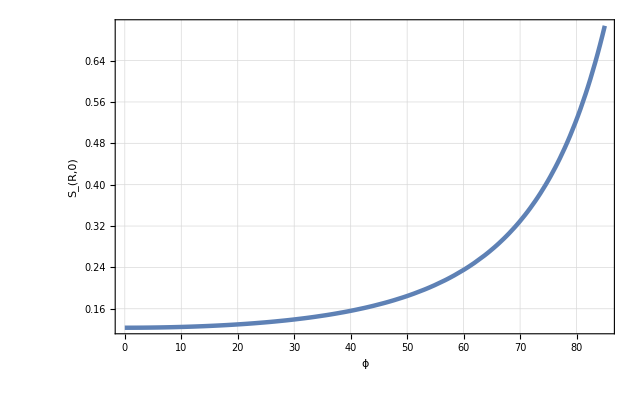

Stokes Vector R.

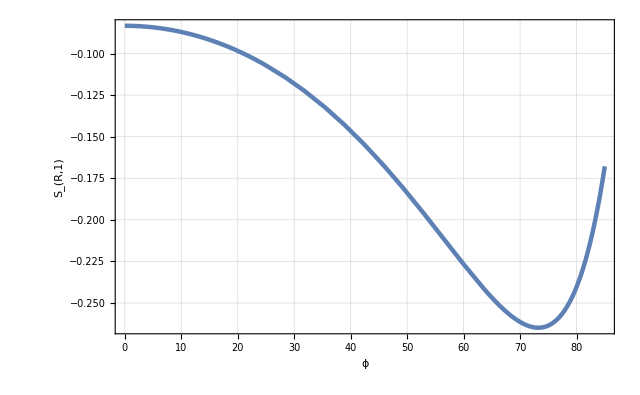

Stokes Vector R.

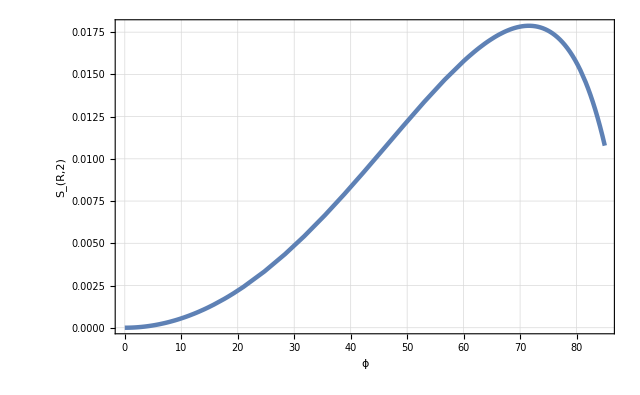

Stokes Vector R.

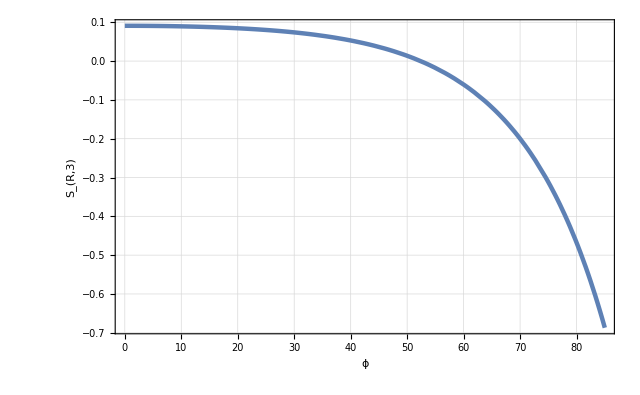

Full intensity of Reflected light.

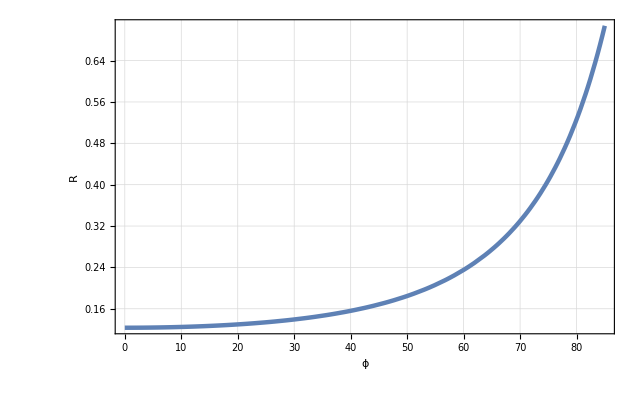

Full intensity of Transmitted light.

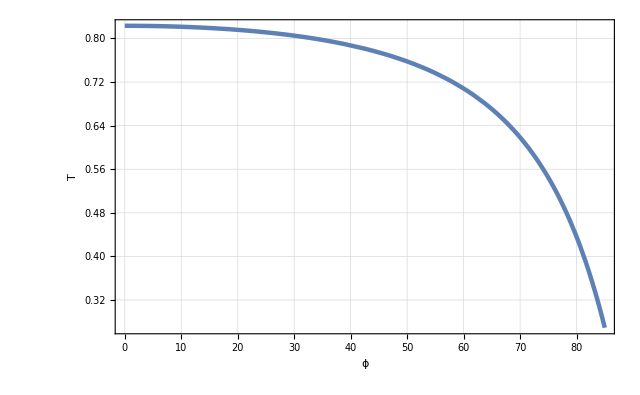

γ of Stokes Vector R.

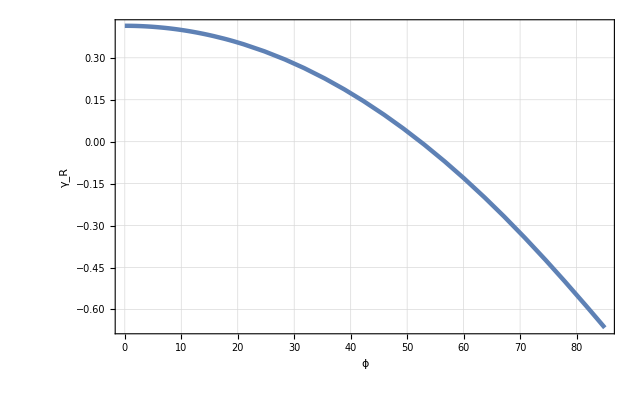

γ of Stokes Vector R (in degrees).

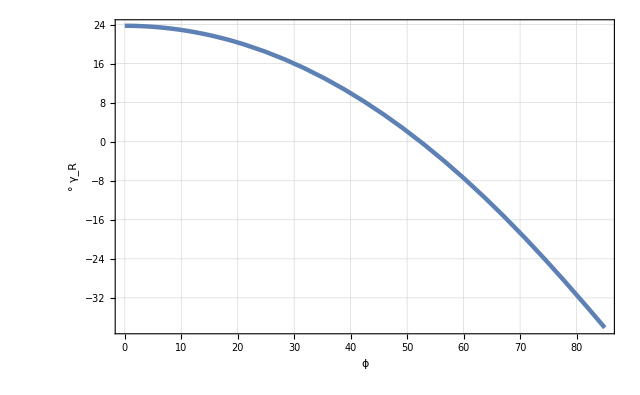

χ of Stokes Vector R.

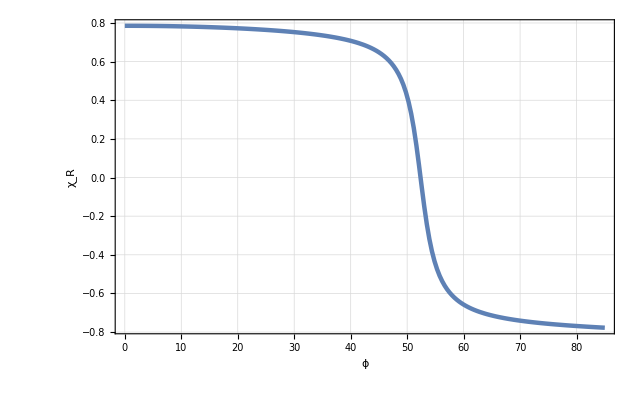

χ of Stokes Vector R (in degrees).

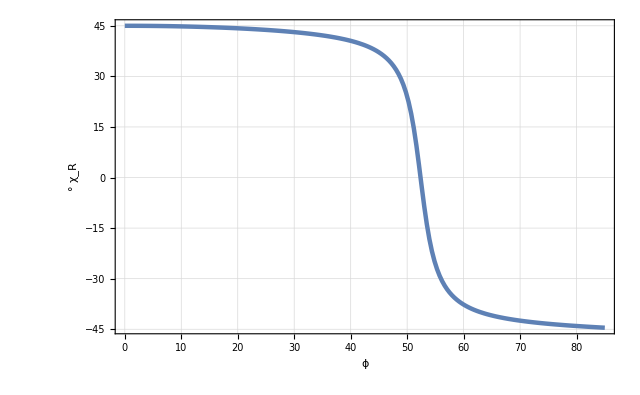

p of Stokes Vector R.

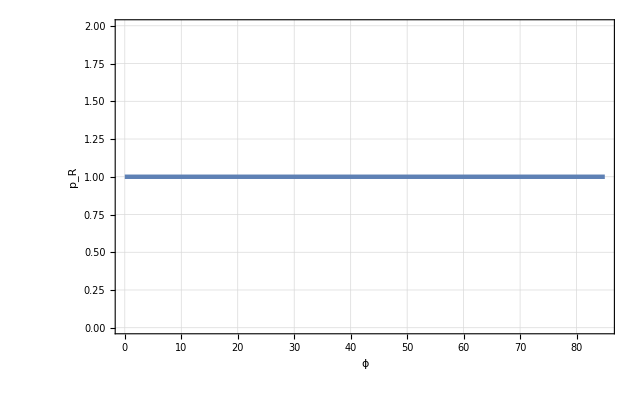

Azimuth of Reflected light in Degrees (new).

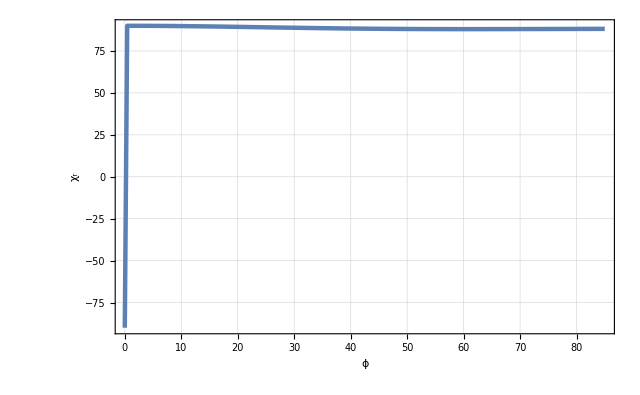

Ellipticity of Reflected light (new).

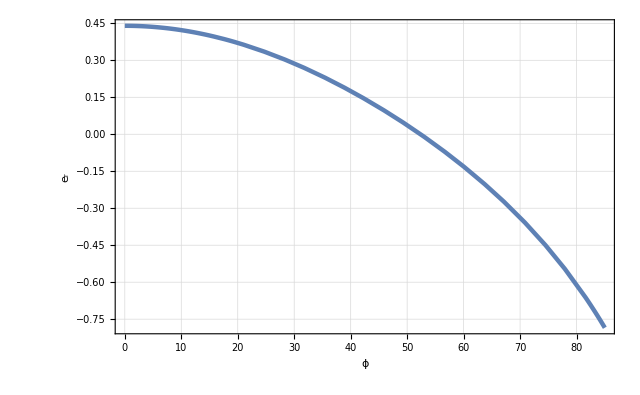

Psi pp in degrees.

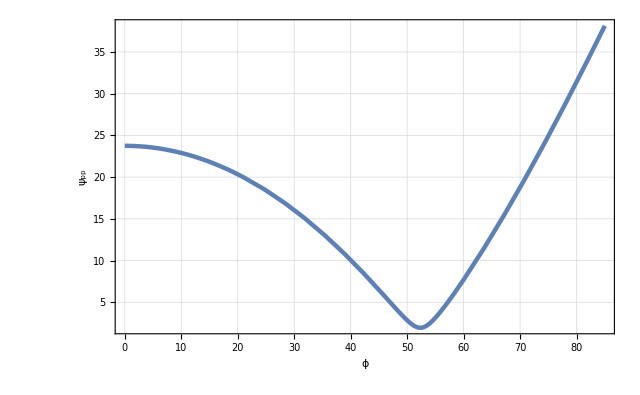

Delta pp in degrees.

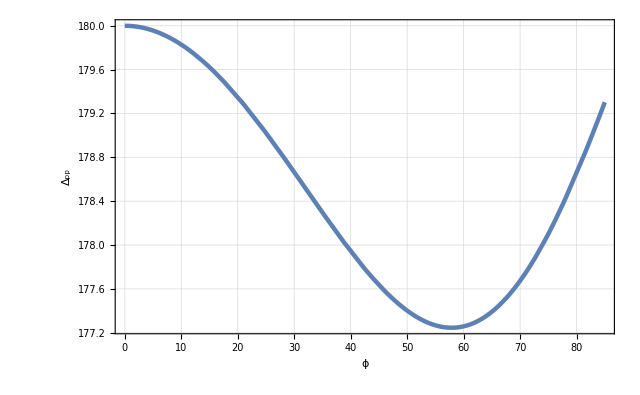

{Intensity of Reflected light going into X component.,Intensity of Reflected light going into Y component.}

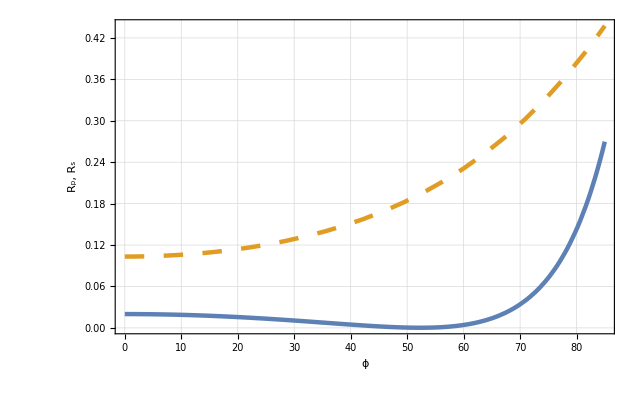

{Intensity of Transmitted light going into X component.,Intensity of Transmitted light going into Y component.}

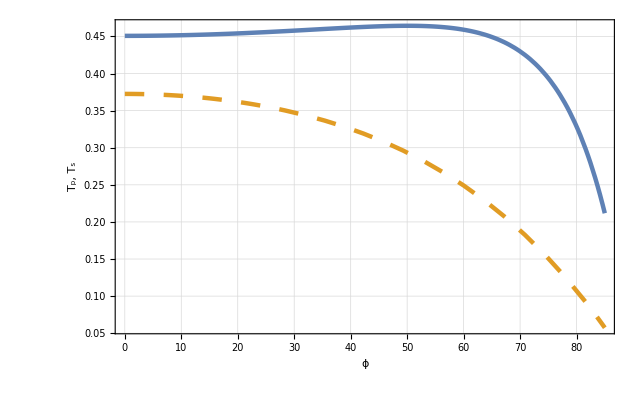

Wed 13 Apr 2016 01:06:44, time used: 1575, total time used: 1641.
---------------------------------------------

```mathematica
(* ============================================== *)
ClearAll["Global`*"];
(* ============================================== *)
PathList={"W:\\Math\\BM\\"};
BaseDir="W:\\Math\\BM\\";
BaseFileName="Example_07";
OutDir=BaseDir<>"Calc\\";
(* ============================================== *)
useParallelTbl=False;
Get["BerremanInit.m",Path-> PathList];
Initialize[PathList, useParallelTbl];
(* ============================================== *)
opts={BDPlotFigures -> True,UseEulerAngles->False};
(* ============================================== *)
(*
FuncList={{StokesVectorI[1],StokesVectorI[2],StokesVectorI[3],StokesVectorI[4]},{StokesVectorR[1],StokesVectorR[2],StokesVectorR[3],StokesVectorR[4]},{EltEG[1],EltEG[2],EltEG[3],EltEG[4]},{XitEGDegree[1],XitEGDegree[2],XitEGDegree[3],XitEGDegree[4]},{IFull,RFull,TFull},{Ix,Iy,Rx,Ry,Tx,Ty},{Eli,Elr,Elt},{XiiDegree, XirDegree,XitDegree},{Sin2Xii,Sin2Xir,Sin2Xit}};
*)

FuncList={StokesVectorR[1],StokesVectorR[2],StokesVectorR[3],StokesVectorR[4],RFull,TFull, StokesGammaR, StokesGammaDegreeR,StokesChiR, StokesChiDegreeR, StokesPolarizedR,XirDegree,Elr,PsiPPDegree,DeltaPPDegree,{Rx,Ry},{Tx,Ty}};

(* ============================================== *)
systemDescription="One Layer biaxial thin film on slighlty absorbing substrate plate.";
Print["!!! For absorbing plate I > R + T !!!"];
(* ============================================== *)
Print["Параметры падающего света..."];
nUpper=1; 

lambda={600,600,1,"λ",nm};fita={0,85,5,"ϕ", Degree};beta={0,0,45,"β", Degree};gamma={0, 0,30,"γ",Degree};
ellipt={-1,1,0.5,"e"};

incidentLight=CreateIncidentRay[nUpper,lambda,fita,beta, ellipt];
OutputIncidentRayInfo[incidentLight];
(* ============================================== *)
Print["Оптические параметры первого тонкого слоя."];
thicknessLayer1={75,75,10,"h",nm};

fiLayer1={0, 0, 30,Subscript["φ","1"], Degree};thetaLayer1={0,0,30,Subscript["θ","1"],Degree};psiLayer1={0,0,30,Subscript["ψ","1"], Degree};
rotationAnglesLayer1={fiLayer1,thetaLayer1,psiLayer1};

epsLayer1=EpsilonFromN[1.50,2.00,1.75];
Print["epsLayer1 = ", epsLayer1 // MatrixForm];

layer1=CreateFilm[thicknessLayer1,rotationAnglesLayer1,epsLayer1];
(* ============================================== *)
Print["Оптические параметры толстой пластинки"];
Print["Для расчетов для различных толщин пластинки нужно поменять значение thickness"];
nSubstr=1.5;
kSubstr=3*10^-6;
thickness=1 mm;
thickPlate=CreateThickPlateFromN[thickness,nSubstr+I* kSubstr];
(* ============================================== *)
Print["Оптические параметры нижней среды..."];
nLower=1.5;
lowerMedia=CreateSemiInfiniteMediaFromN[nLower];
(* ============================================== *)
Print["Создаем оптическую систему..."];
layeredSystem = CreateLayeredSystem[incidentLight,gamma,layer1,thickPlate,lowerMedia];
OutputLayeredSystem[layeredSystem];
(* ============================================== *)
Print["Производим вычисления для различных значений параметров...."];
allCalc=PerformAllCalculations[layeredSystem,FuncList, systemDescription,opts];
(* ============================================== *)
```